## Definitions

```mathematica
Γ3bodytests[mother_,d1_,d2_,d3_,M2_,Sfactor_]:=With[{m0=MASS[mother],m1=MASS[d1],m2=MASS[d2],m3=MASS[d3]},1/((2Pi)^3 32*m0^3)Sfactor*NIntegrate[M2[m12,m23],{m12,m12lower[m1,m2],m12upper[m0,m3]},{m23,m23lower[m12,m0,m1,m2,m3],m23upper[m12,m0,m1,m2,m3]},Method->(*intmethod[process]*)"AdaptiveMonteCarlo"]]
p2body[m_,m1_,m2_]=p/.Solve[√(p^2+m1^2)+√(p^2+m2^2)==m,p][[2]]
replVAP:={θVAPsym[a_,b_]:>Subscript[θ, Row[{a,","b}]]}
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(√(m^4-2 m^2 m1^2-2 m^2 m2^2+m1^4-2 m1^2 m2^2+m2^4))/(2 m)

## Tensor mesons

### Decays of f_2 into a pair of pions

```mathematica
Mdec1=FeynmanRuleVertex0[{"f_2","π^+","π^-"},{1,-1,-1},{"f","π1","π2"}]/.{mt[a_,b_]:>MT[a,b]};
MdecSquared=((Mdec1*(Mdec1/.{ξf1->ϕf1,ξf2->ϕf2})*PolarizationSumTensor["f_2",pf,ξf1,ξf2,ϕf1,ϕf2])//Expand//Contract)/.{pf->pπ1+pπ2}//ExpandScalarProduct//Contract//Simplify;
(*1/5 - number of polarizations of the tensor meson Subscript[f, 2]*)
Print["Squared matrix element:"]
MdecSquared=1/5*MdecSquared/.{ScalarProduct[pf,pf]->mf2^2,ScalarProduct[pπ1,pπ2]->(mf2^2-2 mπ0^2)/2,ScalarProduct[pπ1,pπ1]->mπ0^2,ScalarProduct[pπ2,pπ2]->mπ0^2}//Simplify
Print["Decay width:"]
ΓdecSquared=1/(8*Pi)*MdecSquared/mf2^2(p/.Solve[2 √(mπ0^2+p^2)==mf2,p][[2]]//Quiet)
(*1/2 stays for the contribution from the decay Subscript[f, 2]->2 π^0*)
(1+1/2)ruleSymbolsToNumbersFinal[ΓdecSquared/DECAYWIDTH["f_2"],0.]/.{gT->gTnumeric*10^3}
```

Squared matrix element:

1/60 gT^2 (mf2^2-4 mπ0^2)^2

Decay width:

(gT^2 (mf2^2-4 mπ0^2)^(5/2))/(960 π mf2^2)

0.843504

## Heavy pseudoscalars

### Decays of π^0(1300)

#### ηππ

```mathematica
Γtest=0.;
mother="π^0(1300)";
{d1,d2,d3}={"η","π^+","π^-"};
Mdec1=FeynmanRuleVertex0[{"π^0(1300)",d1,d2,d3},{1,-1,-1,-1},{"πh","η","π1","π2"}]/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit//Simplify;
Mdec1=Mdec1/.{ScalarProduct[pη,pπ1]->(m12-mη^2-mπ0^2)/2,ScalarProduct[pη,pπ2]->(m23-mη^2-mπ0^2)/2}//Simplify;
MsquaredTest[m12_,m23_]=ruleSymbolsToNumbersFinal[Mdec1*ComplexConjugate[Mdec1],2];
Γtest+=Γ3bodytests[mother,d1,d2,d3,MsquaredTest,1]
Mdec1=FeynmanRuleVertex0[{"π^0(1300)","η","π^0","π^0"},{1,-1,-1,-1},{"πh","η","π1","π2"}]/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit//Simplify;
Mdec1=Mdec1/.{ScalarProduct[pη,pπ1]->(m12-mη^2-mπ0^2)/2,ScalarProduct[pη,pπ2]->(m23-mη^2-mπ0^2)/2}/.{ScalarProduct[pπ1,pπ2]->ProductK1K3mandelstam}/.{m1->mπ0,m3->mπ0,m2->mη,m->mπ01300}//Simplify;
MsquaredTest[m12_,m23_]=ruleSymbolsToNumbersFinal[Mdec1*ComplexConjugate[Mdec1],2];
Γtest+=Γ3bodytests[mother,d1,d2,d3,MsquaredTest,1/2]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in m12 near {m12,m23} = {0.999998,0.516446}. NIntegrate obtained 0. and 0. for the integral and error estimates.

0.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in m12 near {m12,m23} = {0.999999,0.232976}. NIntegrate obtained 0. and 0. for the integral and error estimates.

0.

#### KKπ

```mathematica
Γtest=0.;
mother="π^0(1300)";
{d1,d2,d3}={"π^0","K_L","K_S"};
Mdec1=(FeynmanRuleVertex0[{"π^0(1300)",d1,d2,d3},{1,-1,-1,-1},{"πh","π","K1","K2"}])/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit//Simplify;
Mdec1=Mdec1/.{ScalarProduct[pπ,pK1]->(m12-mπ0^2-mKplus^2)/2,ScalarProduct[pπ,pK2]->(m23-mπ0^2-mKplus^2)/2}/.{ScalarProduct[pK1,pK2]->ProductK1K3mandelstam}/.{m1->mKplus,m3->mKplus,m2->mπ0,m->mπ01300}//Simplify;
MsquaredTest[m12_,m23_]=ruleSymbolsToNumbersFinal[Mdec1*ComplexConjugate[Mdec1],2];
Γtest+=Γ3bodytests[mother,d1,d2,d3,MsquaredTest,1]
{d1,d2,d3}={"π^+","K^-","K_S"};
Mdec1=(FeynmanRuleVertex0[{mother,d1,d2,d3},{1,-1,-1,-1},{"πh","π","K1","K2"}])/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit;
Mdec1=Mdec1/.{ScalarProduct[pπ,pK1]->(m12-mπ0^2-mKplus^2)/2,ScalarProduct[pπ,pK2]->(m23-mπ0^2-mKplus^2)/2}/.{ScalarProduct[pK1,pK2]->ProductK1K3mandelstam}/.{m1->mKplus,m3->mKplus,m2->mπ0,m->mπ01300};
MsquaredTest[m12_,m23_]=ruleSymbolsToNumbersFinal[Mdec1*ComplexConjugate[Mdec1],2];
Γtest+=Γ3bodytests[mother,d1,d2,d3,MsquaredTest,1]
Mdec1=(FeynmanRuleVertex0[{"π^0(1300)","π^-","K^+","K_S"},{1,-1,-1,-1},{"πh","π","K1","K2"}])/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit;
{d1,d2,d3}={"π^+","K^-","K_L"};
Mdec1=(FeynmanRuleVertex0[{mother,d1,d2,d3},{1,-1,-1,-1},{"πh","π","K1","K2"}])/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit;
Mdec1=Mdec1/.{ScalarProduct[pπ,pK1]->(m12-mπ0^2-mKplus^2)/2,ScalarProduct[pπ,pK2]->(m23-mπ0^2-mKplus^2)/2}/.{ScalarProduct[pK1,pK2]->ProductK1K3mandelstam}/.{m1->mKplus,m3->mKplus,m2->mπ0,m->mπ01300};
MsquaredTest[m12_,m23_]=ruleSymbolsToNumbersFinal[Mdec1*ComplexConjugate[Mdec1],2];
Γtest+=Γ3bodytests[mother,d1,d2,d3,MsquaredTest,1]
Mdec1=(FeynmanRuleVertex0[{"π^0(1300)","π^-","K^+","K_S"},{1,-1,-1,-1},{"πh","π","K1","K2"}])/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit;
Mdec1=Mdec1/.{ScalarProduct[pπ,pK1]->(m12-mπ0^2-mKplus^2)/2,ScalarProduct[pπ,pK2]->(m23-mπ0^2-mKplus^2)/2}/.{ScalarProduct[pK1,pK2]->ProductK1K3mandelstam}/.{m1->mKplus,m3->mKplus,m2->mπ0,m->mπ01300};
MsquaredTest[m12_,m23_]=ruleSymbolsToNumbersFinal[Mdec1*ComplexConjugate[Mdec1],2];
Γtest+=Γ3bodytests[mother,d1,d2,d3,MsquaredTest,1]
{d1,d2,d3}={"π^0","K^+","K^-"};
Mdec1=(FeynmanRuleVertex0[{"π^0(1300)",d1,d2,d3},{1,-1,-1,-1},{"πh","π","K1","K2"}])/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit;
Mdec1=Mdec1/.{ScalarProduct[pπ,pK1]->(m12-mπ0^2-mKplus^2)/2,ScalarProduct[pπ,pK2]->(m23-mπ0^2-mKplus^2)/2}/.{ScalarProduct[pK1,pK2]->ProductK1K3mandelstam}/.{m1->mKplus,m3->mKplus,m2->mπ0,m->mπ01300};
MsquaredTest[m12_,m23_]=ruleSymbolsToNumbersFinal[Mdec1*ComplexConjugate[Mdec1],2];
Γtest+=Γ3bodytests[mother,d1,d2,d3,MsquaredTest,1]
{d1,d2,d3}={"π^-","K^+","K_S"};
Mdec1=(FeynmanRuleVertex0[{"π^0(1300)",d1,d2,d3},{1,-1,-1,-1},{"πh","π","K1","K2"}])/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit;
Mdec1=Mdec1/.{ScalarProduct[pπ,pK1]->(m12-mπ0^2-mKplus^2)/2,ScalarProduct[pπ,pK2]->(m23-mπ0^2-mKplus^2)/2}/.{ScalarProduct[pK1,pK2]->ProductK1K3mandelstam}/.{m1->mKplus,m3->mKplus,m2->mπ0,m->mπ01300};
MsquaredTest[m12_,m23_]=ruleSymbolsToNumbersFinal[Mdec1*ComplexConjugate[Mdec1],2];
Γtest+=Γ3bodytests[mother,d1,d2,d3,MsquaredTest,1]
{d1,d2,d3}={"π^-","K^+","K_L"};
Mdec1=(FeynmanRuleVertex0[{"π^0(1300)",d1,d2,d3},{1,-1,-1,-1},{"πh","π","K1","K2"}])/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit;
Mdec1=Mdec1/.{ScalarProduct[pπ,pK1]->(m12-mπ0^2-mKplus^2)/2,ScalarProduct[pπ,pK2]->(m23-mπ0^2-mKplus^2)/2}/.{ScalarProduct[pK1,pK2]->ProductK1K3mandelstam}/.{m1->mKplus,m3->mKplus,m2->mπ0,m->mπ01300};
MsquaredTest[m12_,m23_]=ruleSymbolsToNumbersFinal[Mdec1*ComplexConjugate[Mdec1],2];
Γtest+=Γ3bodytests[mother,d1,d2,d3,MsquaredTest,1]
{d1,d2,d3}={"π^0","K_L","K_L"};
Mdec1=(FeynmanRuleVertex0[{"π^0(1300)",d1,d2,d3},{1,-1,-1,-1},{"πh","π","K1","K2"}])/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit;
Mdec1=Mdec1/.{ScalarProduct[pπ,pK1]->(m12-mπ0^2-mKplus^2)/2,ScalarProduct[pπ,pK2]->(m23-mπ0^2-mKplus^2)/2}/.{ScalarProduct[pK1,pK2]->ProductK1K3mandelstam}/.{m1->mKplus,m3->mKplus,m2->mπ0,m->mπ01300};
MsquaredTest[m12_,m23_]=ruleSymbolsToNumbersFinal[Mdec1*ComplexConjugate[Mdec1],2];
Γtest+=Γ3bodytests[mother,d1,d2,d3,MsquaredTest,1/2]
0.002/Γtest
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in m12 near {m12,m23} = {0.999991,0.820631}. NIntegrate obtained 0. and 0. for the integral and error estimates.

0.

0.00150129

0.00198308

0.0034893

0.00349393

0.00501598

0.00549142

0.00549323

0.364085

#### ρπ

```mathematica
Γtest=0.;
mother="π^0(1300)";
{d1,d2}={"ρ^-","π^+"};
Mdec1=PolarizationVector[pρ,ξρ1]*FeynmanRuleVertex0[{"π^0(1300)",d1,d2},{1,-1,-1},{"πh","ρ","π"}]/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit//Contract//Simplify;
Msquared2bodyTest=DoPolarizationSums[Mdec1*ComplexConjugate[Mdec1],pρ]/.{ScalarProduct[pπ,pρ]->(mπ01300^2-mπ0^2-mρ0^2)/2,ScalarProduct[pρ,pρ]->mρ0^2,ScalarProduct[pπ,pπ]->mπ0^2};
Γtest+=Re[ruleSymbolsToNumbersFinal[Msquared2bodyTest/(8Pi)p2body[msymbolic[mother],msymbolic[d1],msymbolic[d2]]/msymbolic[mother]^2//Chop,2]]
{d1,d2}={"ρ^0","π^0"};
Mdec1=PolarizationVector[pρ,ξρ1]*FeynmanRuleVertex0[{"π^0(1300)",d1,d2},{1,-1,-1},{"πh","ρ","π"}]/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit//Contract//Simplify;
Msquared2bodyTest=DoPolarizationSums[Mdec1*ComplexConjugate[Mdec1],pρ]/.{ScalarProduct[pπ,pρ]->(mπ01300^2-mπ0^2-mρ0^2)/2,ScalarProduct[pρ,pρ]->mρ0^2,ScalarProduct[pπ,pπ]->mπ0^2};
Γtest+=Re[ruleSymbolsToNumbersFinal[Msquared2bodyTest/(8Pi)p2body[msymbolic[mother],msymbolic[d1],msymbolic[d2]]/msymbolic[mother]^2//Chop,2]]
{d1,d2}={"ρ^+","π^-"};
Mdec1=PolarizationVector[pρ,ξρ1]*FeynmanRuleVertex0[{"π^0(1300)",d1,d2},{1,-1,-1},{"πh","ρ","π"}]/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit//Contract//Simplify;
Msquared2bodyTest=DoPolarizationSums[Mdec1*ComplexConjugate[Mdec1],pρ]/.{ScalarProduct[pπ,pρ]->(mπ01300^2-mπ0^2-mρ0^2)/2,ScalarProduct[pρ,pρ]->mρ0^2,ScalarProduct[pπ,pπ]->mπ0^2};
Γtest+=Re[ruleSymbolsToNumbersFinal[Msquared2bodyTest/(8Pi)p2body[msymbolic[mother],msymbolic[d1],msymbolic[d2]]/msymbolic[mother]^2//Chop,2]]
0.368/Γtest
```

0.197561

0.197561

0.395122

0.931358

```mathematica
LagrangianGivenFields[{"π^0(1300)","π^+","π^-","π^0"},{1,1,1,1}]//Simplify
θVAPsym["(a^0)_1","π^0"]*θVAPsym["(a^-)_1","π^-"]/.ruleθVAP0explicit
```

coefPheavy π01300(x) (dπminus(x,μ) θVAPsym((a^-)_1,π^-) ((h2star+h3star) π0(x) dπplus(x,μ) θVAPsym((a^+)_1,π^+)-h3star πplus(x) dπ0(x,μ) θVAPsym((a^0)_1,π^0))-h3star πminus(x) dπ0(x,μ) dπplus(x,μ) θVAPsym((a^0)_1,π^0) θVAPsym((a^+)_1,π^+))

(g1^2 ϕN^2)/(ma1^2 (ma1^2-g1^2 ϕN^2))

```mathematica
D[TotalLagrangianScaled,MixCoef]
```

1.26

```mathematica
ruleSymbolsToNumbersFinal[ZP["π^0"],2]
```

1.70913

```mathematica
0.079*1.7^2
```

0.22831

#### 3π

```mathematica
Γtest=0.;
mother="π^0(1300)";
{d1,d2,d3}={"π^+","π^-","π^0"};
Mdec1=(FeynmanRuleVertex0[{"π^0(1300)",d1,d2,d3},{1,-1,-1,-1},{"πh","π1","π2","π3"}])/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit//Simplify;
Mdec1=Mdec1/.{ScalarProduct[pπ1,pπ2]->(m12-2 mπ0^2)/2,ScalarProduct[pπ2,pπ3]->(m23-2 mπ0^2)/2}/.{ScalarProduct[pπ1,pπ3]->ProductK1K3mandelstam}/.{m1->mπ0,m3->mπ0,m2->mπ0,m->mπ01300}//Simplify;
MsquaredTest[m12_,m23_]=ruleSymbolsToNumbersFinal[Mdec1*ComplexConjugate[Mdec1],2];
Γtest+=Γ3bodytests[mother,d1,d2,d3,MsquaredTest,1]
{d1,d2,d3}={"π^0","π^0","π^0"};
Mdec1=(FeynmanRuleVertex0[{"π^0(1300)",d1,d2,d3},{1,-1,-1,-1},{"πh","π1","π2","π3"}])/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit//Simplify;
Mdec1=Mdec1/.{ScalarProduct[pπ1,pπ2]->(m12-2 mπ0^2)/2,ScalarProduct[pπ2,pπ3]->(m23-2 mπ0^2)/2}/.{ScalarProduct[pπ1,pπ3]->ProductK1K3mandelstam}/.{m1->mπ0,m3->mπ0,m2->mπ0,m->mπ01300}//Simplify;
MsquaredTest[m12_,m23_]=ruleSymbolsToNumbersFinal[Mdec1*ComplexConjugate[Mdec1],2];
Γtest+=Γ3bodytests[mother,d1,d2,d3,MsquaredTest,1/6]
```

0.0643639

0.0794117

```mathematica
Lagrπ0ρπ=LagrangianGivenFields[{"π^0(1300)","ρ^-","π^+"},{1,1,1}]+LagrangianGivenFields[{"π^0(1300)","ρ^+","π^-"},{1,1,1}]//Simplify;
Lagrπ0ρπ=Lagrπ0ρπ/.Table[dPfieldSymbol[f,x,μ]->Row[{Subscript[d, μ],",",f}],{f,listMesonP}]/.Table[PheavyFieldSymbol[f,x]->Row[{f}],{f,listMesonPheavy}]/.Table[VfieldSymbol[f,x,μ]->Row[{Superscript[f,"μ"]}],{f,listMesonV}]/.{h3star->Subsuperscript["h","3","*"],ϕN->Subscript[ϕ, N],coefPheavy->1}/.replVAP
θVAP["(a^+)_1","π^+"]/.replVAP/.{g1->Subscript[g, 1],ϕN->Subscript[ϕ, N],ma1->Subscript[m, Subscript[a, 1]],mπplus->Subscript[m, π],Γa1->Subscript[Γ, Subscript[a, 1]]}
```

-ⅈ ϕ_N π^0(1300) h_3^* ((ρ^-)^μ d_μ,π^+ θ_((a^+)_1, π^+)-(ρ^+)^μ d_μ,π^- θ_((a^-)_1, π^-))

-(g_1 m_a_1 ϕ_N)/(√(m_a_1^2-g_1^2 ϕ_N^2))

```mathematica
ruleSymbolsToNumbersFinal[((g1*ϕN)/(ma1^2-mπ0^2))/(g1*ϕN*ma1/(√(ma1^2-g1^2*ϕN^2))),2]
```

0.411628

```mathematica
MASS["(a^+)_1"]
```

1.26

```mathematica
Subscript[g, 1]*Subscript[ϕ, N] 1/Subscript[m^2, Subscript[a, 1]] Subscript[m, Subscript[a, 1]]/(√(Subscript[m^2, Subscript[a, 1]]-Subscript[g^2, 1] Subscript[ϕ^2, N]))
```

(g_1 m_a_1 ϕ_N)/((m^2)_a_1 √((m^2)_a_1-(g^2)_1 (ϕ^2)_N))

### Decays of η(1440) into πKK

```mathematica
θVAPsym["(K^+)_1(1270)","K^+"]/.ruleθVAP0explicit
```

-(g1 sin(θK1) (1-mKplus^2/mK11270^2) (ϕN+√2 ϕS))/(2 (-mK11270^2-ⅈ ΓK11270 mK11270+mKplus^2))

```mathematica
Mdec1=(FeynmanRuleVertex0[{"η(1440)","π^0","K_L","K_S"},{1,-1,-1,-1},{"ηh","π","K1","K2"}])/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit
Mdec1=Mdec1/.{ScalarProduct[pπ,pK1]->(m12-mπ0^2-mKplus^2)/2,ScalarProduct[pπ,pK2]->(m23-mπ0^2-mKplus^2)/2}/.{ScalarProduct[pK1,pK2]->ProductK1K3mandelstam}/.{m1->mKplus,m3->mKplus,m2->mπ0,m->mη1440}//Simplify;
MsquaredTest[m12_,m23_]=ruleSymbolsToNumbersFinal[Mdec1*ComplexConjugate[Mdec1],2];
Γtest=With[{m0=MASS["η(1440)"],m1=MASS["K^+"],m2=MASS["π^0"],m3=MASS["K^+"]},1/((2Pi)^3 32*m0^3)NIntegrate[MsquaredTest[m12,m23],{m12,m12lower[m1,m2],m12upper[m0,m3]},{m23,m23lower[m12,m0,m1,m2,m3],m23upper[m12,m0,m1,m2,m3]},Method->(*intmethod[process]*)"AdaptiveMonteCarlo"]]
```

0

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in m12 near {m12,m23} = {1.,0.563572}. NIntegrate obtained 0. and 0. for the integral and error estimates.

0.

```mathematica
Mdec1=(FeynmanRuleVertex0[{"η(1440)","π^+","K^-","K_S"},{1,-1,-1,-1},{"ηh","π","K1","K2"}])/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit
Mdec1=Mdec1/.{ScalarProduct[pπ,pK1]->(m12-mπ0^2-mKplus^2)/2,ScalarProduct[pπ,pK2]->(m23-mπ0^2-mKplus^2)/2}/.{ScalarProduct[pK1,pK2]->ProductK1K3mandelstam}/.{m1->mKplus,m3->mKplus,m2->mπ0,m->mη1440};
MsquaredTest[m12_,m23_]=ruleSymbolsToNumbersFinal[Mdec1*ComplexConjugate[Mdec1],2];
Γtest=With[{m0=MASS["η(1440)"],m1=MASS["K^+"],m2=MASS["π^0"],m3=MASS["K^+"]},1/((2Pi)^3 32*m0^3)NIntegrate[MsquaredTest[m12,m23],{m12,m12lower[m1,m2],m12upper[m0,m3]},{m23,m23lower[m12,m0,m1,m2,m3],m23upper[m12,m0,m1,m2,m3]},Method->(*intmethod[process]*)"AdaptiveMonteCarlo"]]
```

-(coefPheavy g1^2 h2star ϕN sin^2(θK1) (1-mπplus^2/ma1^2) (1-mK0^2/mK11270^2) (√2 ϕN+2 ϕS) (OverBar[pK2]·OverBar[pπ]))/(8 (-ma1^2-ⅈ Γa1 ma1+mπplus^2) (mK0^2-mK11270^2-ⅈ ΓK11270 mK11270))-(coefPheavy g1^2 h2star ϕN cos^2(θK1) (1-mπplus^2/ma1^2) (1-mK0^2/mK11400^2) (√2 ϕN+2 ϕS) (OverBar[pK2]·OverBar[pπ]))/(8 (-ma1^2-ⅈ Γa1 ma1+mπplus^2) (mK0^2-mK11400^2-ⅈ ΓK11400 mK11400))+(coefPheavy g1^2 h2star ϕN sin^2(θK1) (1-mπplus^2/ma1^2) (1-mKplus^2/mK11270^2) (ϕN+√2 ϕS) (OverBar[pK1]·OverBar[pπ]))/(4 √2 (-ma1^2-ⅈ Γa1 ma1+mπplus^2) (-mK11270^2-ⅈ ΓK11270 mK11270+mKplus^2))+(coefPheavy g1^2 h2star ϕN cos^2(θK1) (1-mπplus^2/ma1^2) (1-mKplus^2/mK11400^2) (ϕN+√2 ϕS) (OverBar[pK1]·OverBar[pπ]))/(4 √2 (-ma1^2-ⅈ Γa1 ma1+mπplus^2) (-mK11400^2-ⅈ ΓK11400 mK11400+mKplus^2))+(coefPheavy g1^2 h3star sin^2(θK1) cos^2(θK1) (1-mK0^2/mK11400^2) (1-mKplus^2/mK11270^2) (√2 ϕN+2 ϕS) (ϕN+√2 ϕS) (OverBar[pK1]·OverBar[pK2]))/(8 (mK0^2-mK11400^2-ⅈ ΓK11400 mK11400) (-mK11270^2-ⅈ ΓK11270 mK11270+mKplus^2))+(coefPheavy g1^2 h3star sin^2(θK1) cos^2(θK1) (1-mK0^2/mK11270^2) (1-mKplus^2/mK11400^2) (√2 ϕN+2 ϕS) (ϕN+√2 ϕS) (OverBar[pK1]·OverBar[pK2]))/(8 (mK0^2-mK11270^2-ⅈ ΓK11270 mK11270) (-mK11400^2-ⅈ ΓK11400 mK11400+mKplus^2))+(coefPheavy g1^2 h3star sin^4(θK1) (1-mK0^2/mK11270^2) (1-mKplus^2/mK11270^2) (√2 ϕN+2 ϕS) (ϕN+√2 ϕS) (OverBar[pK1]·OverBar[pK2]))/(8 (mK0^2-mK11270^2-ⅈ ΓK11270 mK11270) (-mK11270^2-ⅈ ΓK11270 mK11270+mKplus^2))+(coefPheavy g1^2 h3star cos^4(θK1) (1-mK0^2/mK11400^2) (1-mKplus^2/mK11400^2) (√2 ϕN+2 ϕS) (ϕN+√2 ϕS) (OverBar[pK1]·OverBar[pK2]))/(8 (mK0^2-mK11400^2-ⅈ ΓK11400 mK11400) (-mK11400^2-ⅈ ΓK11400 mK11400+mKplus^2))

0.0000628677

```mathematica
Mdec1=(FeynmanRuleVertex0[{"η(1440)","π^-","K^+","K_S"},{1,-1,-1,-1},{"ηh","π","K1","K2"}])/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit;
Mdec1=Mdec1/.{ScalarProduct[pπ,pK1]->(m12-mπ0^2-mKplus^2)/2,ScalarProduct[pπ,pK2]->(m23-mπ0^2-mKplus^2)/2}/.{ScalarProduct[pK1,pK2]->ProductK1K3mandelstam}/.{m1->mKplus,m3->mKplus,m2->mπ0,m->mη1440};
MsquaredTest[m12_,m23_]=ruleSymbolsToNumbersFinal[Mdec1*ComplexConjugate[Mdec1],2];
Γtest=With[{m0=MASS["η(1440)"],m1=MASS["K^+"],m2=MASS["π^0"],m3=MASS["K^+"]},1/((2Pi)^3 32*m0^3)NIntegrate[MsquaredTest[m12,m23],{m12,m12lower[m1,m2],m12upper[m0,m3]},{m23,m23lower[m12,m0,m1,m2,m3],m23upper[m12,m0,m1,m2,m3]},Method->(*intmethod[process]*)"AdaptiveMonteCarlo"]]
```

0.0000635286

```mathematica
θVAPsym["(K^+)_1(1270)","K^+"]/.ruleθVAP0explicit
ruleSymbolsToNumbersFinal[θVAPsym["(K^+)_1(1270)","K^+"]/.ruleθVAP0explicit,0]
```

-(g1 (1-mKplus^2/mK11270^2) (ϕN+√2 ϕS))/(2 (-mK11270^2-ⅈ ΓK11270 mK11270+mKplus^2))

0.617152-0.051521 ⅈ

```mathematica
Mdec1=(FeynmanRuleVertex0[{"η(1440)","π^0","K^+","K^-"},{1,-1,-1,-1},{"ηh","π","K1","K2"}])/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit;
Mdec1=Mdec1/.{ScalarProduct[pπ,pK1]->(m12-mπ0^2-mKplus^2)/2,ScalarProduct[pπ,pK2]->(m23-mπ0^2-mKplus^2)/2}/.{ScalarProduct[pK1,pK2]->ProductK1K3mandelstam}/.{m1->mKplus,m3->mKplus,m2->mπ0,m->mη1440};
MsquaredTest[m12_,m23_]=ruleSymbolsToNumbersFinal[Mdec1*ComplexConjugate[Mdec1],2];
Γtest=With[{m0=MASS["η(1440)"],m1=MASS["K^+"],m2=MASS["π^0"],m3=MASS["K^+"]},1/((2Pi)^3 32*m0^3)NIntegrate[MsquaredTest[m12,m23],{m12,m12lower[m1,m2],m12upper[m0,m3]},{m23,m23lower[m12,m0,m1,m2,m3],m23upper[m12,m0,m1,m2,m3]},Method->(*intmethod[process]*)"AdaptiveMonteCarlo"]]
```

0.0000360794

```mathematica
Mdec1=(FeynmanRuleVertex0[{"η(1440)","π^0","K_L","K_L"},{1,-1,-1,-1},{"ηh","π","K1","K2"}])/.{mt[a_,b_]:>MT[a,b]}/.ruleθVAP0explicit;
Mdec1=Mdec1/.{ScalarProduct[pπ,pK1]->(m12-mπ0^2-mKplus^2)/2,ScalarProduct[pπ,pK2]->(m23-mπ0^2-mKplus^2)/2}/.{ScalarProduct[pK1,pK2]->ProductK1K3mandelstam}/.{m1->mKplus,m3->mKplus,m2->mπ0,m->mη1440};
MsquaredTest[m12_,m23_]=ruleSymbolsToNumbersFinal[Mdec1*ComplexConjugate[Mdec1],2];
Γtest=With[{m0=MASS["η(1440)"],m1=MASS["K^+"],m2=MASS["π^0"],m3=MASS["K^+"]},1/2 1/((2Pi)^3 32*m0^3)NIntegrate[MsquaredTest[m12,m23],{m12,m12lower[m1,m2],m12upper[m0,m3]},{m23,m23lower[m12,m0,m1,m2,m3],m23upper[m12,m0,m1,m2,m3]},Method->(*intmethod[process]*)"AdaptiveMonteCarlo"]]
```

0.0000183696

```mathematica
Mdec1=(FeynmanRuleVertex0[{"η(1440)","π^0","K^+","K^-"},{1,-1,-1,-1},{"ηh","π","K1","K2"}])/.{mt[a_,b_]:>MT[a,b]}/.{coefPheavy->1}//Simplify
Mdec1/.{θVAPsym[a_,b_]:>Subscript[θ, Row[{a,",",b}]]}//Simplify
Mdec1=Mdec1/.ruleθVAP0explicit;
Mdec1=Mdec1/.{ScalarProduct[pπ,pK1]->(m12-mπ0^2-mKplus^2)/2,ScalarProduct[pπ,pK2]->(m23-mπ0^2-mKplus^2)/2}/.{ScalarProduct[pK1,pK2]->ProductK1K3mandelstam}/.{m1->mKplus,m3->mKplus,m2->mπ0,m->mη1440}/.{δ->0}
MsquaredTest[m12_,m23_]=ruleSymbolsToNumbersFinal[Mdec1*ComplexConjugate[Mdec1],2];
Γtest=With[{m0=MASS["η(1440)"],m1=MASS["K^+"],m2=MASS["π^0"],m3=MASS["K^+"]},1/((2Pi)^3 32*m0^3)NIntegrate[MsquaredTest[m12,m23],{m12,m12lower[m1,m2],m12upper[m0,m3]},{m23,m23lower[m12,m0,m1,m2,m3],m23upper[m12,m0,m1,m2,m3]},Method->(*intmethod[process]*)"AdaptiveMonteCarlo"]]
```

1/4 (-θVAPsym((K^+)_1(1270),K^+) ((OverBar[pK2]·OverBar[pπ]) (2 (h2star-2 h3star) θVAPsym(f_1(1420),π^0)+√2 h2star θVAPsym(f_1(1285),π^0)+√2 h2star θVAPsym((a^0)_1,π^0))-2 √2 h3star (OverBar[pK1]·OverBar[pK2]) θVAPsym((K^-)_1(1270),K^-))-(OverBar[pK1]·OverBar[pπ]) θVAPsym((K^-)_1(1270),K^-) (2 (h2star-2 h3star) θVAPsym(f_1(1420),π^0)+√2 h2star θVAPsym(f_1(1285),π^0)+√2 h2star θVAPsym((a^0)_1,π^0)))

1/4 (-θ_((K^+)_1(1270),K^+) ((OverBar[pK2]·OverBar[pπ]) (2 (h2star-2 h3star) θ_(f_1(1420),π^0)+√2 h2star θ_(f_1(1285),π^0)+√2 h2star θ_((a^0)_1,π^0))-2 √2 h3star (OverBar[pK1]·OverBar[pK2]) θ_((K^-)_1(1270),K^-))-(OverBar[pK1]·OverBar[pπ]) θ_((K^-)_1(1270),K^-) (2 (h2star-2 h3star) θ_(f_1(1420),π^0)+√2 h2star θ_(f_1(1285),π^0)+√2 h2star θ_((a^0)_1,π^0)))

1/4 ((g1 (1-mKplus^2/mK11270^2) (ϕN+√2 ϕS) ((g1 h3star (1-mKplus^2/mK11270^2) (ϕN+√2 ϕS) (-m12-m23+mη1440^2+mπ0^2))/(√2 (-mK11270^2-ⅈ ΓK11270 mK11270+mKplus^2))-(g1 h2star ϕN (1-mπ0^2/ma1^2) (m23-mKplus^2-mπ0^2))/(√2 (-ma1^2-ⅈ Γa1 ma1+mπ0^2))))/(2 (-mK11270^2-ⅈ ΓK11270 mK11270+mKplus^2))-(g1^2 h2star ϕN (1-mπ0^2/ma1^2) (1-mKplus^2/mK11270^2) (ϕN+√2 ϕS) (m12-mKplus^2-mπ0^2))/(2 √2 (-ma1^2-ⅈ Γa1 ma1+mπ0^2) (-mK11270^2-ⅈ ΓK11270 mK11270+mKplus^2)))

0.000036731

```mathematica
LagrangianGivenFields[{"η(1440)","π^0","K^+","K^-"},{1,1,1,1}]/.{coefPheavy->1,θVAPsym[a_,b_]:>Subscript[θ, Row[{a,",",b}]]}
(FeynmanRuleVertex0[{"η(1440)","π^0","K_S","K_S"},{1,-1,-1,-1},{"ηh","π","K1","K2"}])/.{mt[a_,b_]:>MT[a,b]}/.{coefPheavy->1,θVAPsym[a_,b_]:>Subscript[θ, Row[{a,",",b}]]}
Mdec1/.{δ->0,coefPheavy->1}
```

-(h3star η1440(x) π0(x) dKminus(x,μ) dKplus(x,μ) θ_((K^-)_1(1270),K^-) θ_((K^+)_1(1270),K^+))/(√2)+(h2star Kplus(x) η1440(x) dKminus(x,μ) dπ0(x,μ) θ_(f_1(1285),π^0) θ_((K^-)_1(1270),K^-))/(2 √2)+1/2 h2star Kplus(x) η1440(x) dKminus(x,μ) dπ0(x,μ) θ_(f_1(1420),π^0) θ_((K^-)_1(1270),K^-)+(h2star Kplus(x) η1440(x) dKminus(x,μ) dπ0(x,μ) θ_((a^0)_1,π^0) θ_((K^-)_1(1270),K^-))/(2 √2)-h3star Kplus(x) η1440(x) dKminus(x,μ) dπ0(x,μ) θ_(f_1(1420),π^0) θ_((K^-)_1(1270),K^-)+(h2star Kminus(x) η1440(x) dKplus(x,μ) dπ0(x,μ) θ_(f_1(1285),π^0) θ_((K^+)_1(1270),K^+))/(2 √2)+1/2 h2star Kminus(x) η1440(x) dKplus(x,μ) dπ0(x,μ) θ_(f_1(1420),π^0) θ_((K^+)_1(1270),K^+)+(h2star Kminus(x) η1440(x) dKplus(x,μ) dπ0(x,μ) θ_((a^0)_1,π^0) θ_((K^+)_1(1270),K^+))/(2 √2)-h3star Kminus(x) η1440(x) dKplus(x,μ) dπ0(x,μ) θ_(f_1(1420),π^0) θ_((K^+)_1(1270),K^+)

1/4 h2star (OverBar[pK1]·OverBar[pπ]+OverBar[pK2]·OverBar[pπ]) θ_(f_1(1285),π^0) θ_((K^0)_1(1270),K_S)-1/4 h2star (OverBar[pK1]·OverBar[pπ]+OverBar[pK2]·OverBar[pπ]) θ_(f_1(1285),π^0) θ_(((K̄)^0)_1(1270),K_S)+(h2star (OverBar[pK1]·OverBar[pπ]+OverBar[pK2]·OverBar[pπ]) θ_(f_1(1420),π^0) θ_((K^0)_1(1270),K_S))/(2 √2)-(h2star (OverBar[pK1]·OverBar[pπ]+OverBar[pK2]·OverBar[pπ]) θ_(f_1(1420),π^0) θ_(((K̄)^0)_1(1270),K_S))/(2 √2)-1/4 h2star (OverBar[pK1]·OverBar[pπ]+OverBar[pK2]·OverBar[pπ]) θ_((K^0)_1(1270),K_S) θ_((a^0)_1,π^0)+1/4 h2star (OverBar[pK1]·OverBar[pπ]+OverBar[pK2]·OverBar[pπ]) θ_(((K̄)^0)_1(1270),K_S) θ_((a^0)_1,π^0)-(h3star (OverBar[pK1]·OverBar[pπ]+OverBar[pK2]·OverBar[pπ]) θ_(f_1(1420),π^0) θ_((K^0)_1(1270),K_S))/(√2)+(h3star (OverBar[pK1]·OverBar[pπ]+OverBar[pK2]·OverBar[pπ]) θ_(f_1(1420),π^0) θ_(((K̄)^0)_1(1270),K_S))/(√2)-√2 h3star (OverBar[pK1]·OverBar[pK2]) θ_((K^0)_1(1270),K_S) θ_(((K̄)^0)_1(1270),K_S)

(g1^2 h2star ϕN (1-mπ0^2/ma1^2) (1-mK0^2/mK11270^2) (√2 ϕN+2 ϕS) (1/2 (m12-mKplus^2-mπ0^2)+1/2 (m23-mKplus^2-mπ0^2)))/(8 (-ma1^2-ⅈ Γa1 ma1+mπ0^2) (mK0^2-mK11270^2-ⅈ ΓK11270 mK11270))+(g1^2 h3star (1-mK0^2/mK11270^2)^2 (√2 ϕN+2 ϕS)^2 (-m12-m23+mη1440^2+mπ0^2))/(16 √2 (mK0^2-mK11270^2-ⅈ ΓK11270 mK11270)^2)

### Decays of π^0(1300) into ρπ

```mathematica
Mdec1=FeynmanRuleVertex0[{"π^0(1300)","ρ^0","π^0"},{1,-1,-1},{"πh","ρ","π"}]
```

0

```mathematica
Mdec1=PolarizationVector[pρ,ξρ1]*FeynmanRuleVertex0[{"π^0(1300)","ρ^+","π^-"},{1,-1,-1},{"πh","ρ","π"}]/.ruleθVAP0explicit//Contract
Msquared2Test=DoPolarizationSums[Mdec1*ComplexConjugate[Mdec1],pρ]/.{ScalarProduct[pπ,pρ]->(msymbolic["π^0(1300)"]^2-mπ0^2-mρplus^2)/2,ScalarProduct[pρ,pρ]->mρplus^2,ScalarProduct[pπ,pπ]->mπ0^2};
Γtest=ruleSymbolsToNumbersFinal[Msquared2Test/(8Pi)*(p/.Solve[√(p^2+mπ0^2)+√(p^2+mρplus^2)==mπ01300,p][[2]])/(msymbolic["π^0(1300)"]^2),0]
```

(coefPheavy g1 h3star ϕN^2 (1-mπplus^2/ma1^2) (OverBar[pπ]·ε̄(pρ)))/(-ma1^2-ⅈ Γa1 ma1+mπplus^2)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

0.0445564+0. ⅈ

```mathematica
Mdec2=PolarizationVector[pρ,ξρ1]*FeynmanRuleVertex0[{"π^0(1300)","ρ^-","π^+"},{1,-1,-1},{"πh","ρ","π"}]/.ruleθVAP0explicit//Contract
Msquared2Test=DoPolarizationSums[Mdec1*ComplexConjugate[Mdec1],pρ]/.{ScalarProduct[pπ,pρ]->(msymbolic["π^0(1300)"]^2-mπ0^2-mρplus^2)/2,ScalarProduct[pρ,pρ]->mρplus^2,ScalarProduct[pπ,pπ]->mπ0^2};
Γtest=ruleSymbolsToNumbersFinal[Msquared2Test/(8Pi)*(p/.Solve[√(p^2+mπ0^2)+√(p^2+mρplus^2)==mπ01300,p][[2]])/(msymbolic["π^0(1300)"]^2),0]
```

-(coefPheavy g1 h3star ϕN^2 (1-mπplus^2/ma1^2) (OverBar[pπ]·ε̄(pρ)))/(-ma1^2-ⅈ Γa1 ma1+mπplus^2)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

0.0445564+0. ⅈ

```mathematica
(V[x,a]^2/2+a*V[x,a]*dP[x,a])/.{V[x,a]->V[x,a]-a*dP[x,a]}//Expand
```

1/2 (V(x,a))^2-1/2 a^2 (dP(x,a))^2

```mathematica
h3starval
```

35.

```mathematica
θVAPsym["(a^+)_1","π^+"]/.ruleθVAP0explicit
```

-(g1 ϕN (1-mπplus^2/ma1^2))/(-ma1^2-ⅈ Γa1 ma1+mπplus^2)

```mathematica
ruleSymbolsToNumbersFinal[θVAPsym["(a^+)_1","π^+"]/.ruleθVAP0explicit,2]
```

0.507139-0.223713 ⅈ

### Decays of η(1440) into KK^*

```mathematica
PolarizationVector[pKstar,ξKstar1]*FeynmanRuleVertex0[{"η(1440)","K^(*+)","K^-"},{1,-1,-1},{"ηh","Kstar","K"}]/.{θVAPsym[a_,b_]:>Subscript[θ, Row[{a,","b}]]}//Contract
```

(coefPheavy h3star ϕN (OverBar[pK]·ε̄(pKstar)) θ_((K^+)_1(1270), K^+))/(√2)

```mathematica
θVAPsym["(K^+)_1(1270)","K^+"]/.ruleθVAP0explicit
```

-(g1 (1-mKplus^2/mK11270^2) (ϕN+√2 ϕS))/(2 (-mK11270^2-ⅈ ΓK11270 mK11270+mKplus^2))

```mathematica
Mdec1=PolarizationVector[pKstar,ξKstar1]*FeynmanRuleVertex0[{"η(1440)","K^(*+)","K^-"},{1,-1,-1},{"ηh","Kstar","K"}]/.ruleθVAP0explicit//Contract
Msquared2Test=DoPolarizationSums[Mdec1*ComplexConjugate[Mdec1],pKstar]/.{ScalarProduct[pK,pKstar]->(msymbolic["η(1440)"]^2-mKplus^2-mKstarplus^2)/2,ScalarProduct[pKstar,pKstar]->mKstarplus^2,ScalarProduct[pK,pK]->mKplus^2};
Γtest=ruleSymbolsToNumbersFinal[Msquared2Test/(8Pi)*(p/.Solve[√(p^2+mKplus^2)+√(p^2+mKstarplus^2)==mη1440,p][[2]])/msymbolic["η(1440)"]^2,0]
Mdec1=PolarizationVector[pKstar,ξKstar1]*FeynmanRuleVertex0[{"η(1440)","K^(*0)","K_S"},{1,-1,-1},{"ηh","Kstar","K"}]/.ruleθVAP0explicit//Contract
Msquared2Test=DoPolarizationSums[Mdec1*ComplexConjugate[Mdec1],pKstar]/.{ScalarProduct[pK,pKstar]->(msymbolic["η(1440)"]^2-mKplus^2-mKstarplus^2)/2,ScalarProduct[pKstar,pKstar]->mKstarplus^2,ScalarProduct[pK,pK]->mKplus^2};
Γtest=ruleSymbolsToNumbersFinal[Msquared2Test/(8Pi)*(p/.Solve[√(p^2+mKplus^2)+√(p^2+mKstarplus^2)==mη1440,p][[2]])/msymbolic["η(1440)"]^2,0]
Mdec1=PolarizationVector[pKstar,ξKstar1]*FeynmanRuleVertex0[{"η(1440)","K^(*0)","K_L"},{1,-1,-1},{"ηh","Kstar","K"}]/.ruleθVAP0explicit//Contract
Msquared2Test=DoPolarizationSums[Mdec1*ComplexConjugate[Mdec1],pKstar]/.{ScalarProduct[pK,pKstar]->(msymbolic["η(1440)"]^2-mKplus^2-mKstarplus^2)/2,ScalarProduct[pKstar,pKstar]->mKstarplus^2,ScalarProduct[pK,pK]->mKplus^2};
Γtest=ruleSymbolsToNumbersFinal[Msquared2Test/(8Pi)*(p/.Solve[√(p^2+mKplus^2)+√(p^2+mKstarplus^2)==mη1440,p][[2]])/msymbolic["η(1440)"]^2,0]
Mdec1=PolarizationVector[pKstar,ξKstar1]*FeynmanRuleVertex0[{"η(1440)","(K̄)^(*0)","K_L"},{1,-1,-1},{"ηh","Kstar","K"}]/.ruleθVAP0explicit//Contract
Msquared2Test=DoPolarizationSums[Mdec1*ComplexConjugate[Mdec1],pKstar]/.{ScalarProduct[pK,pKstar]->(msymbolic["η(1440)"]^2-mKplus^2-mKstarplus^2)/2,ScalarProduct[pKstar,pKstar]->mKstarplus^2,ScalarProduct[pK,pK]->mKplus^2};
Γtest=ruleSymbolsToNumbersFinal[Msquared2Test/(8Pi)*(p/.Solve[√(p^2+mKplus^2)+√(p^2+mKstarplus^2)==mη1440,p][[2]])/msymbolic["η(1440)"]^2,0]
```

-(coefPheavy g1 h3star ϕN (1-mKplus^2/mK11270^2) (ϕN+√2 ϕS) (OverBar[pK]·ε̄(pKstar)))/(2 √2 (-mK11270^2-ⅈ ΓK11270 mK11270+mKplus^2))

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

0.00212201+0. ⅈ

(coefPheavy g1 h3star ϕN (1-mK0^2/mK11270^2) (√2 ϕN+2 ϕS) (OverBar[pK]·ε̄(pKstar)))/(4 √2 (mK0^2-mK11270^2-ⅈ ΓK11270 mK11270))

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

0.00106096+1.35525×10^-20 ⅈ

-(coefPheavy g1 h3star ϕN (1-mK0^2/mK11270^2) (√2 ϕN+2 ϕS) (OverBar[pK]·ε̄(pKstar)))/(4 √2 (mK0^2-mK11270^2-ⅈ ΓK11270 mK11270))

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

0.00106096+1.35525×10^-20 ⅈ

(coefPheavy g1 h3star ϕN (1-mK0^2/mK11270^2) (√2 ϕN+2 ϕS) (OverBar[pK]·ε̄(pKstar)))/(4 √2 (mK0^2-mK11270^2-ⅈ ΓK11270 mK11270))

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

0.00106096+1.35525×10^-20 ⅈ

```mathematica
Mdec2=PolarizationVector[pρ,ξρ1]*FeynmanRuleVertex0[{"π^0(1300)","ρ^-","π^+"},{1,-1,-1},{"πh","ρ","π"}]/.ruleθVAP0explicit//Contract
Msquared2Test=DoPolarizationSums[Mdec1*ComplexConjugate[Mdec1],pρ]/.{ScalarProduct[pπ,pρ]->(msymbolic["π^0(1300)"]^2-mπ0^2-mρplus^2)/2,ScalarProduct[pρ,pρ]->mρplus^2,ScalarProduct[pπ,pπ]->mπ0^2};
Γtest=ruleSymbolsToNumbersFinal[Msquared2Test/(8Pi)*(p/.Solve[√(p^2+mπ0^2)+√(p^2+mρplus^2)==mπ01300,p][[2]])/(msymbolic["π^0(1300)"]^2),0]
```

-(coefPheavy g1 h3star ϕN^2 (1-mπplus^2/ma1^2) (OverBar[pπ]·ε̄(pρ)))/(-ma1^2-ⅈ Γa1 ma1+mπplus^2)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

0.0445564+0. ⅈ

```mathematica
(V[x,a]^2/2+a*V[x,a]*dP[x,a])/.{V[x,a]->V[x,a]-a*dP[x,a]}//Expand
```

1/2 (V(x,a))^2-1/2 a^2 (dP(x,a))^2

```mathematica
h3starval
```

35.

```mathematica
θVAPsym["(a^+)_1","π^+"]/.ruleθVAP0explicit
```

-(g1 ϕN (1-mπplus^2/ma1^2))/(-ma1^2-ⅈ Γa1 ma1+mπplus^2)

```mathematica
ruleSymbolsToNumbersFinal[θVAPsym["(a^+)_1","π^+"]/.ruleθVAP0explicit,2]
```

0.507139-0.223713 ⅈ

### Decay width into a pair of photons

#### Test - 1: comparison with 2110.10698

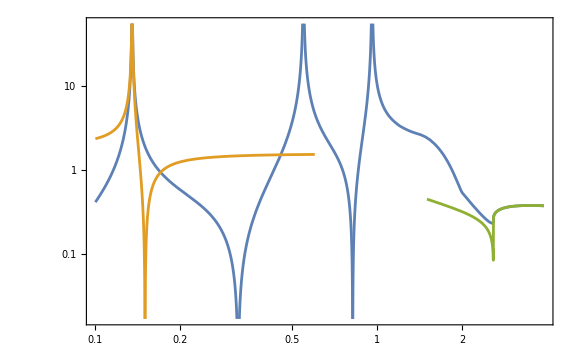

```mathematica
Do[
crgval[ALPcouplingslist[[i]]]=cRGval["Gluon",10^3,ALPcouplingslist[[i]]]
,{i,1,Length[ALPcouplingslist],1}];
rgflow=Table[crgval[ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
(*The Subscript[c, γγ] coupling smoothly glued between the ChPT regime and the QCD perturbative regime*)
cγglued[ma_]=cγGluing[ma,10^3,crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],crgval["ce"],crgval["cμ"],crgval["cτ"]];
(*Eq. 2.72 from https://arxiv.org/pdf/2110.10698.pdf*)
cγγEffChRotation[ma_]=If[ma<MASS["η'"],Evaluate[-((2/3(4κmatrixStandard[[1]][[1]]+κmatrixStandard[[2]][[2]]+κmatrixStandard[[3]][[3]])/.{mu->MASS["u"],md->MASS["d"],ms->MASS["s"]})-0.08)crgval["cG"]],0];
cγγNeubertLow[ma_]=cγγEffChRotation[ma]-ma^2/(MASS["π^0"]^2-ma^2)*(δval+crgval["cu"]-crgval["cd"])+(2*3*Sum[Symbol["c"<>q]*CHARGE[q]^2 LoopFactor[(4*MASS[q]^2)/ma^2],{q,{"c","b"}}]/.Table[Symbol["c"<>q]->crgval["c"<>q],{q,{"u","d","s","c","b"}}]);
cγγNeubertHigh[ma_]=Abs[(2*3*Sum[Symbol["c"<>q]*CHARGE[q]^2 LoopFactor[(4*MASS[q]^2)/ma^2],{q,{"u","d","s","c","b"}}]/.Table[Symbol["c"<>q]->crgval["c"<>q],{q,{"u","d","s","c","b"}}])+(cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,10^3,"Loop c_G"]/.Table[Symbol["c"<>q]->crgval["c"<>q],{q,{"u","d","s","c","b"}}]/.{cG->1})];
LogLogPlot[{Quiet[cγglued[ma]],If[ma<0.6,Evaluate[Abs[cγγNeubertLow[ma]]],0],If[ma>1.5,Quiet[Evaluate[Abs[cγγNeubertHigh[ma]]]],0]},{ma,0.1,3.9},Frame->True,ImageSize->Large]
```

#### Test - 2

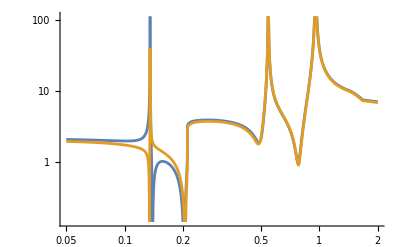

```mathematica
Do[
crgval[ALPcouplingslist[[i]]]=cRGval["Fermion universal",10^3,ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
rgflow=Table[crgval[ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
(*The Subscript[c, γγ] coupling smoothly glued between the ChPT regime and the QCD perturbative regime*)
cγglued1[ma_]=cγGluing[ma,10^3,crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],crgval["ce"],crgval["cμ"],crgval["cτ"]];
Do[crgval[ALPcouplingslist[[i]]]=cRGval["Fermion universal",MASS["t"],ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
rgflow=Table[crgval[ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
(*The Subscript[c, γγ] coupling smoothly glued between the ChPT regime and the QCD perturbative regime*)
cγglued2[ma_]=cγGluing[ma,MASS["t"],crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],crgval["ce"],crgval["cμ"],crgval["cτ"]];
LogLogPlot[Evaluate[{cγglued1[ma],cγglued2[ma]}],{ma,0.05,2}]
```

#### Test - 3: comparison with 1811.03474

1/((ma^2-1. mη^2) (ma^2-1. mηpr^2) (ma^2-1. mπ0^2))0.362887 ((4.44089×10^-16 κd+4.44089×10^-16 κu-0.0915605) ma^6+((-4.44089×10^-16 κd-4.44089×10^-16 κu+1.29596) mη^2+mηpr^2 (-4.44089×10^-16 κd-4.44089×10^-16 κu+1.092)+mπ0^2 (0.0457803 δ-4.44089×10^-16 κd-4.44089×10^-16 κu-2.20484)) ma^4+((1.37784 δ+2.2964) mπ0^4+mηpr^2 (-0.474539 δ+4.44089×10^-16 κd+4.44089×10^-16 κu+0.132746) mπ0^2+mη^2 ((4.44089×10^-16 κd+4.44089×10^-16 κu-2.2964) mηpr^2+mπ0^2 (-0.949079 δ+4.44089×10^-16 κd+4.44089×10^-16 κu-0.224307))) ma^2+mηpr^2 mπ0^4 (-0.918559 δ-1.22474)+mη^2 mπ0^2 ((1.37784 δ-4.44089×10^-16 κd-4.44089×10^-16 κu+2.2964) mηpr^2+mπ0^2 (-0.459279 δ-1.07165))) If[ma<2.98838,InterpolatingFunction[…](ma),3.75226/ma^4]

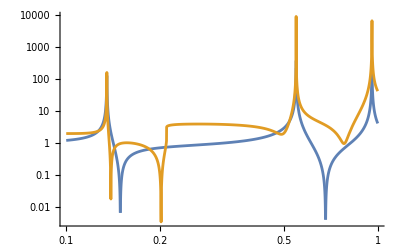

1/9 (-(9 ((-((cu-cd) ϵ ma^2)-(2 ((cs-cu) ma^2-cd ma^2) mπ0^2 δ ϵ)/(3 (ma^2-mη^2))+((cd ma^2+(2 cs+cu) ma^2) mπ0^2 δ ϵ)/(3 (ma^2-mηpr^2)))/(ma^2-mπ0^2)+(cG ((mπ0^2 (2 ma^2-mηpr^2-mπ0^2) δ ϵ)/(3 (ma^2-mηpr^2))-(2 mπ0^2 (ma^2-2 mη^2+mπ0^2) δ ϵ)/(3 (ma^2-mη^2))))/(ma^2-mπ0^2)+cG ϵ (κd-κu)))/ϵ-6 cG (3 κu+1)-(4 √6 ((cG (√(2/3) ϵ ma^2+√(2/3) (mπ0^2-2 mη^2) ϵ))/(ma^2-mη^2)+(-√(2/3) (cd-cs+cu) ϵ ma^2-(√(2/3) (cd-cu) mπ0^2 δ ϵ ma^2)/(ma^2-mπ0^2))/(ma^2-mη^2)-2 √(2/3) cG ϵ (κd+κu)))/ϵ-(7 √3 (-(cG (2 ma^2-mηpr^2-mπ0^2) ϵ)/(√3 (ma^2-mηpr^2))+(cG (κd+κu) ϵ)/(√3)+(-((cd-cu) ma^2 δ ϵ mπ0^2)/(√3 (ma^2-mπ0^2))-((cd ma^2+(2 cs+cu) ma^2) ϵ)/(√3))/(ma^2-mηpr^2)))/ϵ) If[ma<2.98838,InterpolatingFunction[…](ma),3.75226/ma^4]

```mathematica
Do[crgval[ALPcouplingslist[[i]]]=cRGval["Gluon 1811.03474",10^3,ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
(*cγglued1[ma_]=cγGluing[ma,10^3,crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],crgval["ce"],crgval["cμ"],crgval["cτ"]];*)
Do[crgval[ALPcouplingslist[[i]]]=cRGval["Gluon 1811.03474",10^3,ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
quantity1[ma_]=cγγEfftemp/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription]/.Table[x->crgval[ToString[x]],{x,{cu,cd,cs,cc,cb,ct,cG}}]//Simplify
quantity1[ma_]=ruleSymbolsToNumbers[quantity1[ma],choiceMixingDescription,2];
LogLogPlot[{Abs[quantity1[ma]],cγglued1[ma]},{ma,0.1,1},PlotRange->All]
```

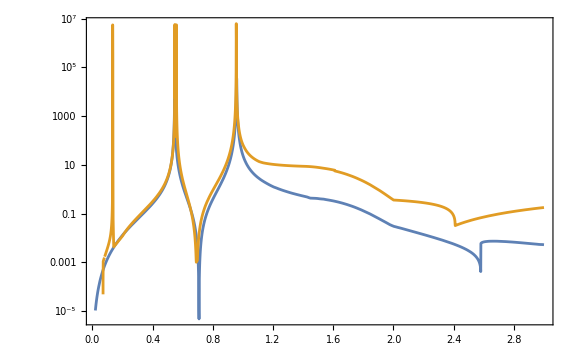

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\Temp\notebooks\phenomenology\temp\GammaTo2gamma.txt

```mathematica
cγγEff[ma_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,ce_,cμ_,cτ_,"VMD"]=ruleSymbolsToNumbers[cγγEfftemp,"No π^0-η/η' mixing",0];
Do[crgval[ALPcouplingslist[[i]]]=cRGval["Gluon 1811.03474",10^3,ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
cγglued1[ma_]=cγGluing[ma,10^3,crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],crgval["ce"],crgval["cμ"],crgval["cτ"]];
ΓALPto2γ[ma_,fa_]=1/2 1/(8Pi)M2numeric2body["2γ",ma,fa,crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],cγglued1[ma],crgval["ce"],crgval["cμ"],crgval["cτ"]] 1/(2ma);
(*Decay width into photons from Fig. S1 from https://arxiv.org/pdf/1811.03474*)
ΓALPto2γAloni[ma_]=If[ma<=0.071,0,Evaluate[Interpolation[Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology","external data","GammaTo2gammaAloni.txt"}],"Table"],InterpolationOrder->1][ma]]];
(*Conversion coefficients from Subscript[f, a] in https://arxiv.org/pdf/1811.03474 to Subscript[f, a] in this notebook*)
GeVtoeV=10^9;
CoefffaConversionToAloni=GeVtoeV(32. Pi^2)^2;
LogPlot[{CoefffaConversionToAloni*ΓALPto2γ[ma,10^3],If[ma<0.550,Evaluate[ΓALPto2γAloni[ma]],Evaluate[ΓALPto2γAloni[ma-0.01]]]},{ma,0.02,3},PlotRange->All,ImageSize->Large,Frame->True,FrameStyle->Directive[Thick,Black,18]]
Export[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"phenomenology","external data","GammaTo2gamma.txt"}],Table[{ma,CoefffaConversionToAloni*ΓALPto2γ[ma,10^3]},{ma,0.02,3,0.001}],"Table"]
cγγEff[ma_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,ce_,cμ_,cτ_,"VMD"]=symbolsToNumbersWidths[cγγEfftemp];
```